```mathematica
L =5;
b = 1/10; 
h = 1/10; 
EE = 200*10^9; 
q = 10;
F = 1000;

Izz = b*h^3/12;

reg= Region[Parallelepiped[{-L/2,-h/2,-b/2},{{L,0,0},{0,h,0},{0,0,b}}]];

u[X_, Y_, Z_] :={-Y*Sin[ArcTan[y'[X]]],y[X] + Y*(Cos[ArcTan[y'[X]]]-1),0 }
```

## One end fixed

```mathematica
equation = {D[EE*Izz*D[y[x],x,x],x,x]==q};
conditions = {y[-L/2]==0,y'[-L/2]==0,y''[L/2]==0,y'''[L/2]==-F/(EE*Izz)};
sol = DSolve[Join[equation,conditions],y[x],{x,-L/2,L/2}]
```

{{y[x]→((5+2 x)^2 (20425-1660 x+4 x^2))/64000000}}

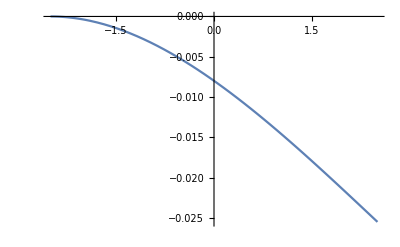

```mathematica
Plot[-y[x]/.sol,{x,-L/2,L/2}]
```

```mathematica
VectorDisplacementPlot3D[Flatten[u[x, y, z] /. sol],{x, y, z}∈reg, AxesLabel->{x, y, z}, PlotPoints->40, ImageSize->Large,ViewPoint->{0,0,1}]
```

-Graphics3D-

## Both ends fixed

```mathematica
conditions2={y[-L/2]==0,y'[-L/2]==0,y[L/2]==0,y'[L/2]==0};
```

```mathematica
sol2 = DSolve[Join[equation,conditions2],y[x],{x,-L/2,L/2}]
```

{{y[x]→((25-4 x^2)^2)/64000000}}

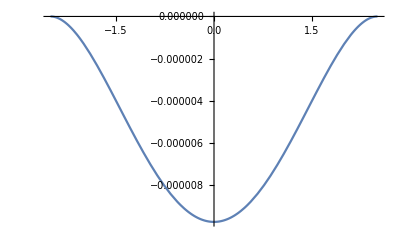

```mathematica
Plot[-y[x]/.sol2,{x,-L/2,L/2}]
```

## Wooden beam - both ends fixed

wood

WolframAlphaQueryResults

```mathematica
Ew=9.4*10^9;
Lw=10;
equationw = {D[Ew*Izz*D[y[x],x,x],x,x]==q};
conditionsw={y[-Lw/2]==0,y'[-Lw/2]==0,y[Lw/2]==0,y'[Lw/2]==0};
```

```mathematica
solw=DSolve[Join[equationw,conditionsw],y[x],{x,-Lw/2,Lw/2}]
```

{{y[x]→0.00332447+1.0842×10^-19 x-0.000265957 x^2-3.46945×10^-21 x^3+5.31915×10^-6 x^4}}

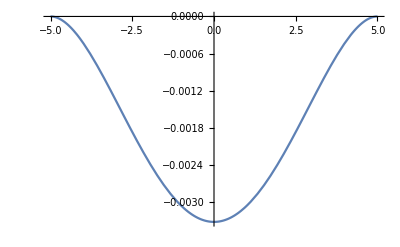

```mathematica
Plot[-y[x]/.solw,{x,-Lw/2,Lw/2}]
```